## Integration Test

Define a set of functions to be integrated

Define a set of intervals on which `NIntegrate` should be performed

Measure the timing performance of both version of Mathematica

```mathematica
myFunction[k_,a_]:=Sum[i*a*Sin[#]^i,{i,k,0,-1}]&[x];
functionGrupx[n_,a_]:=Table[myFunction[k,a][x],{k,1,n}];
t25=Table[i,{i,1,25,1}];
t55=Table[i,{i,1,50,1}];
t75=Table[i,{i,1,75,1}];
```

### Create threaded operation

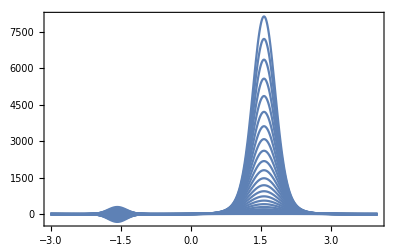

```mathematica
thop[lister_]:=MapThread[myFunction,{lister,lister}];
Plot[thop[t25],{x,-3,4},PlotRange->Full,Frame->True,Axes->False]
```